# “Cadena de favores”

En la película (y el libro) “cadena de favores”, plantean la siguiente estrategia para hacer más agradable a la comunidad: si alguien te hace un favor, en lugar de regresar el favor para que la cuenta quede saldada, haces favores (que no pudieran hacer elles mismes) a otras tres personas (diferentes a quien te ayudó en primera instancia). La idea es que haya un efecto dominó donde la gente se ayuda sin esperar algo a cambio.

Podemos modelar este problema como un sistema dinámico para poder determinar:
1) Bajo qué condiciones la gente termina olvidando el movimiento.
2) Bajo qué condiciones el movimiento podría sobrevivir.
3) La fracción de la población que participa en el movimiento si éste sobrevive.
4) Cuál es la cantidad mínima de personas que deben iniciar el movimiento.

Como hablamos de “supervivencia” y “poblaciones”, podemos modelar este movimiento mediante una ecuación diferencial, igual que en dinámica de poblaciones. El modelo sugerido es el siguiente:

donde  es el número de personas que participan en el movimiento, y  es la población total, que supondremos constante. Podemos interpretar cada uno de los términos para entender cuales son las suposiciones del modelo:
1) - es un término de disminución. Modela el hecho de que eventualmente las personas se olvidan del movimiento. Supone una tasa de olvido constante .
2)  es la fracción de la población total que NO está en el movimiento.
3)  es el número de personas que SÍ está en el movimiento.
4)  es la tasa de convencimiento per cápita.
Este modelo también es muy similar a los modelos epidemiológicos, así que el primer término, que es el más complicado, lo podemos interpretar haciendo un símil epidemiológico.  representa el número de encuentros exitosos entre personas en el movimiento con personas fuera del movimiento (excluye contactos entre dos personas fuera y entre dos personas dentro del movimiento), similar a los contactos entre sanos e infectados. El término  es análogo a la infectividad, que mide la probabilidad con la que estos encuentros resultan en la persona fuera del movimiento convencida en participar en él. A diferencia de los modelos epidemiológicos, esta cantidad no es constante, sino que es una función de , pues suponemos que mientras más personas haya en el movimiento, más familiar estará la persona a convencer con el movimiento, y más fácil su convencimiento.

Dado que  es una probabilidad, su crecimiento debe estar acotado. Para tomar en cuenta esta restricción, se consideran dos funciones que muestran el fenómeno de “saturación”, donde  crece con  hasta mantenerse casi constante en un valor límite. Haremos el análisis con cada una de estas formas funcionales de .

## Primera forma

En primera instancia, consideramos la forma funcional
,
donde  y  sson constantes positivas. Fácilmente, vemos que , por lo que  es el supremo de los posibles valores de , lo cual modela la susceptibilidad innata de la gente a ser convencida. Adicionalmente, vemos que , por lo que  es el número de personas necesarias en el movimiento para que la probabilidad de convencimiento alcance la mitad de su valor máximo. Por lo tanto, si  es pequeño, es fácil convencer a la gente aún con pocas personas participando al movimiento, mientras que si  es grande, es difícil convencer a las personas a menos de que el movimiento sea considerablemente grande.

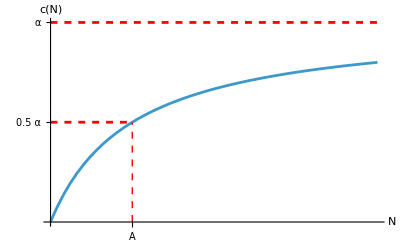

```mathematica
Show[Plot[x/(5+x),{x,0,20},AxesLabel->{"N",c["N"]},PlotRange->All,Ticks->{{{5,A}},{{0.5,0.5α},{1,α}}},Epilog->{Directive[{Red,Dashed}],Line[{{5,0},{5,0.5}}]}],Plot[1,{x,0,20},PlotStyle->{Red,Dashed}],Plot[0.5,{x,0,5},PlotStyle->{Red,Dashed}]]
```

En este caso, tenemos la ecuación diferencial , donde

Pra responder las preguntas que hicimos antes, hacemos el análisis de estabilidad. Empezamos calculando las soluciones de equilibrio:

Automáticamente vemos que  es una solución de equilibrio. Dejando de lado esta solución, las demás soluciones de equilibrio deben cumplir:

Multiplicando en todos lados por  y haciendo un poco de álgebra, llegamos a la ecuación
, 
la cual podemos usar con la fórmula cuadrática, obteniendo

De inmediato vemos que las soluciones no son reales, es decir, no existen si
,
y las dos soluciones se fusionan y son iguales a  cuando
, 
es decir, éste es el punto de una bifuración de silla-nodo (pues un punto de equilibrio aparece de la nada y se divide en dos). Despejando  podemos encontrar el punto de bifurcación respecto a :

Vemos que todos los parámetros están involucrados en esta igualdad, por lo que todos son bifurcantes. Nos gustaría saber cuál de los puntos de equilibrio (el que tiene signo más o el que tiene menos) es el estable y cuál es el inestable. Sin embargo, calcular la estabilidad de éstos es complicado. Contraintuitivamente, podemos deducirlo calculando la estabilidad del equilibrio trivial.
Para calcular la estabilidad necesitamos , dada por

inmediatamente vemos que 
.
Como  es un parámetro positivo, vemos que el cero siempre es estable. Recordando que, en un punto de equilibrio estable, la gráfica del espacio fase cruza el eje horizontal de arriba hacia abajo, y vice versa en un punto de equilibrio inestable, deducimos que el siguiente punto de equilibrio después del cero es inestable, y el que le sigue es estable (piensa porqué, tiene que ver con la continuidad de , que es continua para todo , lo cual siempre se cumple porque no hay números negativos de personas). Deducimos entonces que 
 es inestable y
 es estable.
Finalmente, podemos responder las preguntas que nos hicimos anteriormente.
1) Dado que antes de la bifurcación, i.e. para , el único punto de equilibrio que existe es  y es estable, entonces sólo superando esta condición el movimiento puede sobrevivir. 
2) Si se supera la condición anterior, se necesitan al menos  personas que inicien el movimiento, ya que hasta aquí llega la cuenca de atracción del cero.
3) Si las dos condiciones anteriores se cumplen, entonces el movimiento sobrevivirá y después de mucho tiempo, habremos convencido a un número , pues este es el punto de equilibrio no trivial.
Es buena idea que confirmen estos resultados haciendo experimentos numéricos en la parta de debajo:

```mathematica
a=1;
P=30;
m=0.5;
```

```mathematica
f1[n_,A_]:=(a*n/(n+A))*n*(P-n)/P-m*n;
```

```mathematica
Manipulate[Plot[f1[x,A],{x,3,13},PlotRange->{Automatic,{-1,1}},AxesLabel->{"N",OverDot["N"]}],{A,2.5,5}]
```

```mathematica
t1=Table[{A,n/.FindRoot[f1[n,A]==0,{n,12}]},{A,2.5,3.749,0.001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
t2=Table[{A,n/.FindRoot[f1[n,A]==0,{n,4}]},{A,2.5,3.749,0.001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

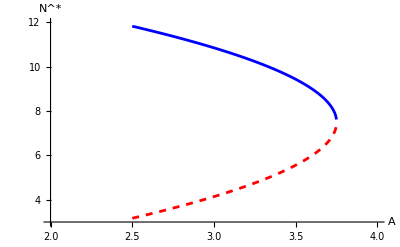

```mathematica
Show[ListPlot[t1,PlotRange->{{2,4},{3,12}},Joined->True,PlotStyle->Blue,AxesLabel->{A,SuperStar["N"]}],ListPlot[t2,PlotRange->{{2,4},{3,12}},Joined->True,PlotStyle->{Red,Dashed}]]
```

## Segunda forma

En segunda instancia, consideramos la forma funcional

lo cual nos dice que, si , , mientras que si , . Su gráfica se ve como

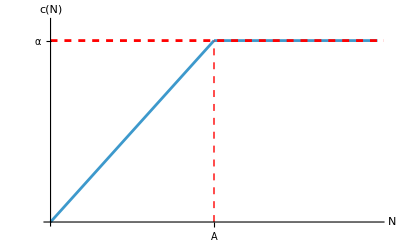

```mathematica
Show[Plot[x/5,{x,0,5},AxesLabel->{"N",c["N"]},PlotRange->{{0,10},{0,1.1}},Ticks->{{{5,A}},{{1,α}}},Epilog->{Directive[{Red,Dashed}],Line[{{5,0},{5,1}}]}],Plot[1,{x,5,10}],Plot[1,{x,0,20},PlotStyle->{Red,Dashed}]]
```

Otra vez vemos que  es la probabilidad de convencimiento máxima y  es el número de personas necesarias en el movimiento para que la probabilidad de convencimiento sea máxima. Mientras más chico , menos personas son necesarias para tener una gran probabilidad de convencimiento, y vice versa.
Dado que esta es una función definida a trozos, el análisis también debe hacerse a trozos.
Empezamos por el caso más fácil, si , entonces  y tenemos que 

Al calcular los puntos de equilibrio, vemos de inmediato que  es una solución de equilibrio. Sin embargo, este caso no es realista, pues necesitamos que  y como  es un número positivo de personas, tenemos que , por lo que no caemos en este caso. Eliminando esta posibilidad, necesitamos que 
,
por lo que la solución de equilibrio es . Vemos que esta solución de equilibrio sólo es realista si , de otro modo es negativa y no representa una población real. Calculando su estabilidad tenemos que 
.
Evaluando , tenemos 
.
Pero dijimos que para que esta solución fuera realista, , por lo que , y siempre es estable. Por lo tanto nunca hay bifurcación en este caso. Pero podemos concluir que, si  (si hay más personas en el movimiento que la cantidad necesaria para tener un convencimiento máximo) y si , es decir que la probabilidad de convencimiento es mayor a la probabilidad de olvido, entonces el movimiento podría sobrevivir, con un número  en el movimiento después de mucho tiempo.
Ahora consideramos el caso . En este caso  y tenemos que

Naturalmente, un punto de equilibrio es , el cual sí tiene sentido en este caso. Los otros puntos de equilibrio obedecen la ecuación algebraica 

lo cual resulta en dos puntos de equilibrio

De nuevo, el punto de bifurcación se da cuando los dos se fusionan y tienen el valor . Esto pasa cuando , es decir, en el valor crítico de 
. Por lo tanto, éste es el criterio para que el movimiento pueda sobrevivir si el número de personas no es suficiente para alcanzar la probabilidad de convencimiento máxima. Para calcular su estabilidad, podemos aplicar un criterio similar al del caso anterior. Calculamos la estabilidad del cero usando la derivada,

Evaluando en cero, vemos que al igual que la foma anterior,
,
por lo que  siempre es estable, y por lo tanto  es inestable y  es estable. Dado que en este caso  no es complicado, podemos corroborar estas conclusiones evaluando los dos puntos de equilibrio, obteniendo

donde se usó la ecuación  que cumplen los puntos de equilibrio (¿puedes ver cómo?) para simplificar la expresión. Como todos los parámetros, así como el número de personas, son números positivos, la estabilidad de los puntos de equilibrio depende de . Una sencilla sustitución muestra que  es inestable y  es positiva.

```mathematica
a=0.7;
P=30;
m=0.3;
```

```mathematica
f2[n_,A_]:=Piecewise[{{(a*n/A)*n*(P-n)/P-m*n,n<A},{a*n*(P-n)/P-m*n,n>=A}}];
```

```mathematica
Manipulate[Plot[f2[x,A],{x,9,19},PlotRange->{Automatic,{-1,1}},AxesLabel->{"N",OverDot["N"]}],{A,16,19}]
```

```mathematica
t3=Table[{A,n/.FindRoot[f2[n,A]==0,{n,12}]},{A,16,17.5,0.001}];
t4=Table[{A,n/.FindRoot[f2[n,A]==0,{n,17}]},{A,16,17.5,0.001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

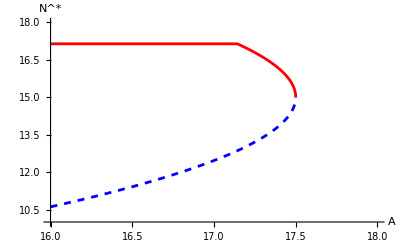

```mathematica
Show[ListPlot[t3,PlotRange->{{16,18},{10,18}},Joined->True,PlotStyle->{Blue,Dashed},AxesLabel->{A,SuperStar["N"]}],ListPlot[t4,PlotRange->{{16,18},{10,18}},Joined->True,PlotStyle->Red]]
```